# ODT painting

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[ListPlot,Joined->True,PlotStyle->Thickness[0.005],Frame->True,GridLines->Automatic,ImageSize->Medium];
SetOptions[ListLogPlot,Joined->True,PlotStyle->Thickness[0.005],Frame->True,GridLines->Automatic,ImageSize->Medium];
SetOptions[Plot,PlotStyle->Thickness[0.005],Frame->True,GridLines->Automatic,ImageSize->400];
SetOptions[LogPlot,PlotStyle->Thickness[0.005],Frame->True,GridLines->Automatic,ImageSize->Medium];
```

## Standard Gaussian trap

```mathematica
trap[x_,y_]:=Exp[-(2 x^2+2 y^2)]
```

```mathematica
α = 7 Degree//N
ep = 0.001;
```

0.122173

```mathematica
traptimeavg[x_,dx_,y_]:=NIntegrate[trap[x-dx Sin[2π t],y],{t,0,1}] (*sine modulation*)
```

```mathematica
traptimeavg[x_,dx_,y_]:=NIntegrate[trap[x-dx (t-0.5),y],{t,0,1}](*sawtooth modulation*)
```

```mathematica
lim=5;
```

```mathematica
disp = 5;
```

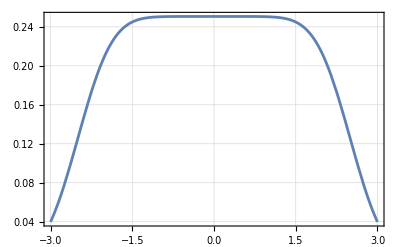

```mathematica
Plot[traptimeavg[x,disp,0],{x,-3,3}]
```

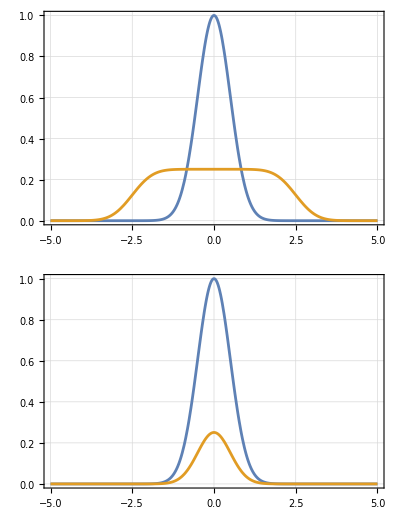

```mathematica
GraphicsColumn[{Plot[{traptimeavg[x,0,0],traptimeavg[x,disp,0]},{x,-lim,lim},PlotRange->{0,1}],Plot[{traptimeavg[0,0,y],traptimeavg[0,disp,y]},{y,-lim,lim},PlotRange->{0,1}]}]
```

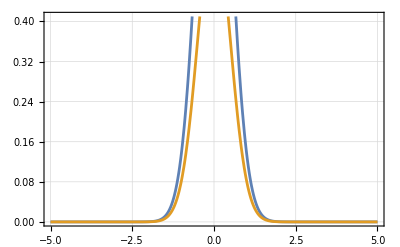

```mathematica
Plot[{traptimeavg[0,0,y],traptimeavg[0,2,y]},{y,-lim,lim}]
```

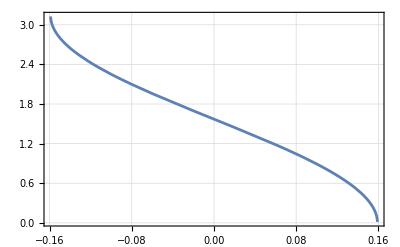

```mathematica
Plot[ArcCos[2π t],{t,-1,1},PlotRange->All]
```

## Crossed beam ODT

```mathematica
cdttrap[x_,y_]:=Exp[-(2((x-ArcTan[α] y)/Cos[α]^2)^2)]+Exp[-(2((x+ArcTan[α] y)/Cos[α]^2)^2)](*assuiming infinite rayleigh range*)
```

```mathematica
cdtraptimeavg[x_,dx_,y_]:=NIntegrate[cdttrap[x-dx (t-0.5),y],{t,0,1}](*sawtooth translation in x-direction*)
```

```mathematica
plim=10;
```

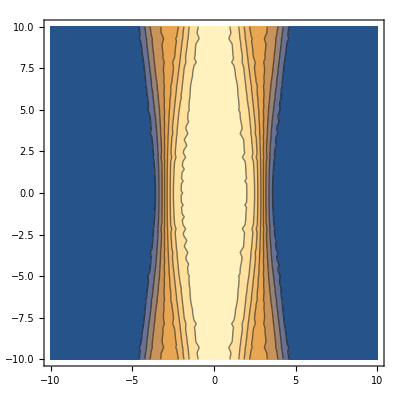

```mathematica
ContourPlot[cdtraptimeavg[x,6,y],{x,-plim,plim},{y,-plim, plim},PlotRange->All]
```

#### 2D potentials for 0,1,4,6 waists modulation depth

```mathematica
GraphicsRow[Table[ContourPlot[cdtraptimeavg[x,dd,y],{x,-plim,plim},{y,-plim, plim},PlotRange->All],{dd,{0,1,4,6}}]]
```

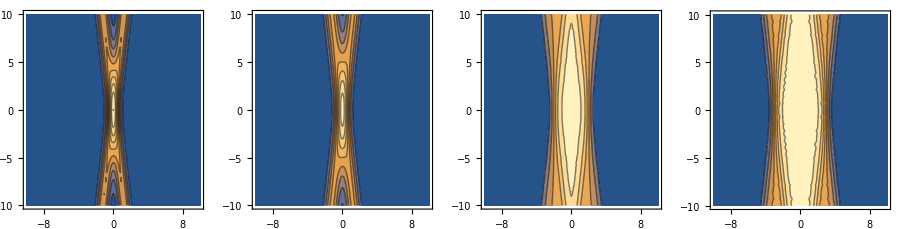

#### Transverse cuts for 0,1,4,6 waists modulation

Plot along y axis (propagation direction)

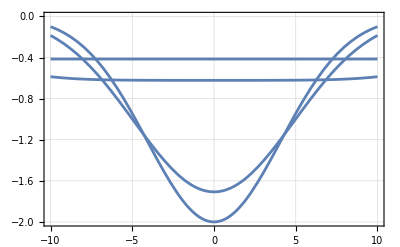

```mathematica
Plot[Table[-cdtraptimeavg[0,dd,y],{dd,{0,1,4,6}}],{y,-plim, plim}]
```

Plot along x axis (transverse to beam direction)

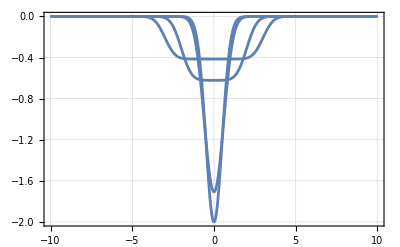

```mathematica
Plot[Table[-cdtraptimeavg[x,dd,0],{dd,{0,1,4,6}}],{x,-plim, plim},PlotRange->All]
```

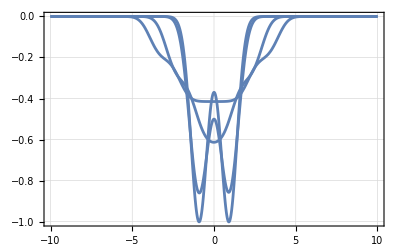

```mathematica
Plot[Table[-cdtraptimeavg[x,dd,7.5],{dd,{0,1,4,6}}],{x,-plim, plim},PlotRange->All]
```